# 9.3

```mathematica
(*Vamos trabalhar com L=1 e v=1*)
```

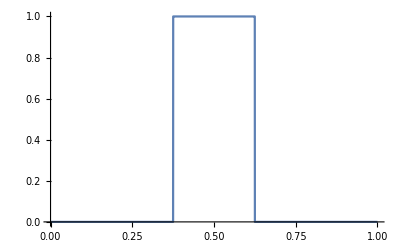

```mathematica
Func[x_]=HeavisidePi[4(x-1/2)](*Pulso Inicial*);
Plot[Func[x],{x,0,1},Exclusions->None (*Para plotar a derivada descontínua*)]
```

```mathematica
(*Serie de Fourier: Subscript[Σ, n] Subscript[A, n] Cos(Subscript[k, n] x) + Subscript[B, n] Sin(Subscript[k, n] x);
Escolhemos Subscript[A, n] = 0 pelas condições fronteira;
Subscript[k, n]=nπ;*)
```

```mathematica
$Assumptions= n ∈ Integers
Integrate[Sin[n π x]^2,{x,0,1}]
```

n∈ℤ

1/2

```mathematica
(*Logo,*)
Bm[m_]=2Integrate[Sin[m π x]Func[x],{x,0,1}]
```

(2 (Cos[(3 m π)/8]-Cos[(5 m π)/8]))/(m π)

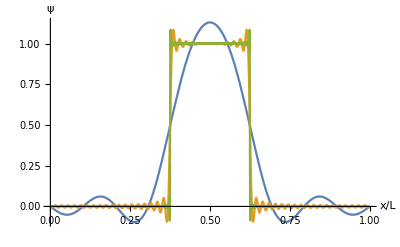

```mathematica
Plot[{Sum[Bm[m]Sin[m π x],{m,1,10}],Sum[Bm[m]Sin[m π x],{m,1,100}],Sum[Bm[m]Sin[m π x],{m,1,1000}]},{x,0,1},AxesLabel->{"x/L","ψ"}](*Pode demorar um pouco (mexam no numero de termos a somar se demorar muito); Vejam como a série converge para a função quando se adicionam mais termos*)
```

```mathematica
(*ω=v*k=nπ , nas nossas unidades*)
```

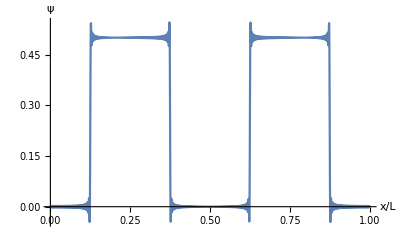

```mathematica
Plot[Sum[Bm[m]Sin[m π x]Cos[ m π t]/.t->1/4 (*Inserimos a dependencia temporal*),{m,1,500}],{x,0,1},AxesLabel->{"x/L","ψ"}]
```

```mathematica
(*O pulso separa-se em 2, um a viajar para a direita e outro para a esquerda, e após t=L/(4v) eles percorreram x=1/4 nas nossas unidades*)
```

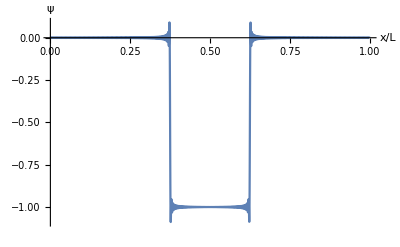

```mathematica
Plot[Sum[Bm[m]Sin[m π x]Cos[ m π t]/.t->1 (*Inserimos a dependencia temporal*),{m,1,500}],{x,0,1},AxesLabel->{"x/L","ψ"}]
```

```mathematica
(*Os dois pulsos voltam a unir-se com uma diferença de fase de π*)
```